# Efficient Water - Cooled Bitter - Type Electromagnet for Zeeman Slowing in Cold - Atom Experiments

## Rishav Koirala and Ben A. Olsen 2025

## Impedance Measurement

CSV files with AC current response are stored in the directory impedance_data, in two sets: 
1) filenames beginning with s are measuring a standard resistor, instead of the ZS coil, to calibrate out effects of the measurement circuit. 
1) filenames beginning with ZS are measuring the ZS coil.
Each filename contains the ac frequency in Hz.

In each CSV, the relevant columns are 4: the time, 5: the sense resistor voltage, and 11: the ZS/calibration resistor voltage.

We fit both voltages as functions of time with sinusoidal functions with the same frequency, but different amplitudes, offsets, and phases.

The ratio of the resulting best-fit amplitudes (normalized by the sense resistor resistance) gives the impedance of the coil/calibration resistor at that frequency

```mathematica
npoints = 130;
Measure[filename_, frequency_, inamplitude_, inoffset_,outamplitude_, outoffset_, inplotrange_, outplotrange_]:=
(Module[{},data = Import[StringJoin[NotebookDirectory[],"/impedance_data/",filename, ".csv"], "Data"];

 timesRaw = Table[data[[jj]][[4]], {jj, Length[data]}];
VinRaw = Table[data[[jj]][[5]], {jj, Length[data]}];
VoutRaw = Table[data[[jj]][[11]], {jj, Length[data]}];
(*offset = 1.6, amplitude = 0.7 *)
Vin = Transpose@{timesRaw, VinRaw};
Vout = Transpose@{timesRaw, VoutRaw};
fitVin = NonlinearModelFit[Vin, Vin0 Sin[2π f t + ϕ1] + c1, {{Vin0, inamplitude}, {f, frequency}, {ϕ1, 0}, {c1, inoffset}}, t, Method->"LevenbergMarquardt"];
fitVout = NonlinearModelFit[Vout, Vout0 Sin[2π f t + ϕ2] + c2, {{Vout0, outamplitude}, {f, frequency}, {ϕ2, 0}, {c2, outoffset}}, t, Method->"LevenbergMarquardt"];

(* Input Voltage Amplitude *)
Vin0fit =Vin0/.fitVin["BestFitParameters"][[1]];
Vin0err = (fitVin["ParameterConfidenceIntervals"][[1]][[2]]-fitVin["ParameterConfidenceIntervals"][[1]][[1]])/4;

(* Input Phase *)
ϕ1fit =ϕ1/.fitVin["BestFitParameters"][[3]];
ϕ1err = (fitVin["ParameterConfidenceIntervals"][[3]][[2]]-fitVin["ParameterConfidenceIntervals"][[3]][[1]])/4;

(* Output Voltage Amplitude *)
Vout0fit =Vout0/.fitVout["BestFitParameters"][[1]];
Vout0err = (fitVout["ParameterConfidenceIntervals"][[1]][[2]]-fitVout["ParameterConfidenceIntervals"][[1]][[1]])/4;

(* Output Phase *)
ϕ2fit =ϕ2/.fitVout["BestFitParameters"][[3]];
ϕ2err = (fitVout["ParameterConfidenceIntervals"][[3]][[2]]-fitVout["ParameterConfidenceIntervals"][[3]][[1]])/4;

Vratio = Abs[Vout0fit/Vin0fit];
(*CellPrint@ExpressionCell[Show[ListPlot[Vin, PlotStyle-> LightOrange], Plot[fitVin[t], {t, -inplotrange, inplotrange}, PlotStyle->{Dashed,Red}, PlotLabel->"Input", PlotPoints->npoints]]];
CellPrint@ExpressionCell[Show[ListPlot[Vout, PlotStyle->LightBlue], Plot[fitVout[t], {t, -outplotrange, outplotrange}, PlotStyle->{Dashed,Purple}, PlotLabel->"Input",  PlotPoints->npoints]]];*)
result = {frequency, Vin0fit, Vin0err, ϕ1fit, ϕ1err, Vout0fit, Vout0err, ϕ2fit, ϕ2err, Vratio}]
)
```

```mathematica
(* Import standard resistor impedance *)
S01=Measure["s0.1", 0.1, 1, 1, 0.2, 0.3, 10., 10.];
S02=Measure["s0.2", 0.2,1, 1, 0.2, 0.3, 10., 10.];
S05=Measure["s0.5", 0.5, 1, 1, 0.2, 0.3, 10., 10.];
S1=Measure["s1", 1, 1, 1, 0.2, 0.3, 0.4, 0.4];
S2=Measure["s2", 2,1, 1, 0.2, 0.3, 0.4, 0.4];
S5=Measure["s5", 5, 1, 1, 0.2, 0.3, 0.4, 0.4];
S10=Measure["s10", 10, 1, 1, 0.2, 0.3, 0.4, 0.4];
S20=Measure["s20", 20, 1, 1, 0.2, 0.3, 0.4, 0.4];
S50=Measure["s50", 50, 1, 1, 0.2, 0.3, 0.4, 0.4];
S100=Measure["s100", 100, 1, 1, 0.2, 0.3, 0.4, 0.4];
S200=Measure["s200", 200, 1, 1, 0.2, 0.3, 0.4, 0.4];
S500=Measure["s500", 500, 1, 1, 0.2, 0.3, 0.4, 0.4];
S1000=Measure["s1000", 1000,1, 1, 0.2, 0.3, 0.4, 0.4];
S2000=Measure["s2000", 2000, 1, 1, 0.2, 0.3, 0.0003, 0.0003];
S5000=Measure["s5000", 5000, 1, 1, 0.2, 0.3, 0.00005, 0.00005];
S10000=Measure["s10000", 10000, 1, 1, 0.2, 0.3, 0.00005, 0.00005];
```

```mathematica
(* Beta value *)

standardResistance = 0.1;

betas = {S01[[10]],S02[[10]],S05[[10]],S1[[10]],S2[[10]],S5[[10]],S10[[10]],S20[[10]],S50[[10]],S100[[10]],S200[[10]],S500[[10]],S1000[[10]],S2000[[10]],S5000[[10]]}/standardResistance;

β = Mean[betas]
βerr  = StandardDeviation[betas]+ 0.05*standardResistance
```

2.92914

0.0171941

```mathematica
(* Import ZS impedance *)
ZS01=Measure["0.1", 0.1, 0.4, 0.6, 0.05, 0.04, 10, 10];
ZS02=Measure["0.2", 0.2,  0.4, 0.6, 0.05, 0.04, 5, 5];
ZS05=Measure["0.5", 0.5,  0.4, 0.6, 0.05, 0.04, 5, 5];
ZS1=Measure["1", 1,  0.4, 0.6, 0.05, 0.04, 2, 2];
ZS2=Measure["2", 2,  0.4, 0.6, 0.05, 0.04, 2, 2];
ZS5=Measure["5", 5,  0.4, 0.6, 0.05, 0.04, 1, 1];
ZS10=Measure["10", 10,  0.4, 0.6, 0.05, 0.04, 1, 1];
ZS20=Measure["20", 20,  0.4, 0.6, 0.05, 0.04, 0.4, 0.4];
ZS50=Measure["50", 50, 0.4, 0.6, 0.05, 0.04, 0.4, 0.4];
ZS100=Measure["100", 100,  0.4, 0.6, 0.05, 0.04, 0.4, 0.4];
ZS200=Measure["200", 200, 0.4, 0.6, 0.05, 0.04, 0.4, 0.4];
ZS500=Measure["500", 500,  0.5, 0.6, 0.115, 0.009, 0.4, 0.4];
ZS1000=Measure["1000", 1000,  0.5, 0.6, 0.20, -0.04, 0.4, 0.4];
ZS2000=Measure["2000", 2000, 0.5, 0.6, 0.4, -0.13, 0.001, 0.001];
ZS5000=Measure["5000", 5000,  0.5, 0.62, 0.8, 0.5, 0.006, 0.004];
ZS10000=Measure["10000", 10000,  0.5, 0.6, 1.9, 0.2, 0.006, 0.004];
```

Once we have fit each of the ac responses, we assemble all the data for fitting with the LR lumped-circuit model, and plot the data along with the best-fit impedance curve

{{0.1,24.8338},{0.2,24.6798},{0.5,25.0505},{1,24.922},{2,25.0096},{5,25.226},{10,25.0571},{20,25.5083},{50,26.9459},{100,31.114},{200,41.0878},{500,75.0389},{1000,134.008},{2000,251.734},{5000,599.905},{10000,1204.01}}

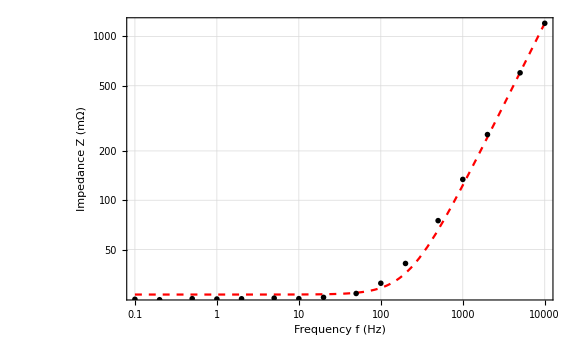

{R→26.5426,L→0.0191844}

{3.28291,0.000148754}

```mathematica
Vin0s = {ZS01[[2]], ZS02[[2]],ZS05[[2]],ZS1[[2]],ZS2[[2]],ZS5[[2]],ZS10[[2]],
ZS20[[2]],ZS50[[2]],ZS100[[2]],ZS200[[2]],ZS500[[2]],ZS1000[[2]],ZS2000[[2]],
ZS5000[[2]],ZS10000[[2]]};
Vin0errs ={ZS01[[3]], ZS02[[3]],ZS05[[3]],ZS1[[3]],ZS2[[3]],ZS5[[3]],ZS10[[3]],
ZS20[[3]],ZS50[[3]],ZS100[[3]],ZS200[[3]],ZS500[[3]],ZS1000[[3]],ZS2000[[3]],
ZS5000[[3]],ZS10000[[3]]};
Vout0s = {ZS01[[6]], ZS02[[6]],ZS05[[6]],ZS1[[6]],ZS2[[6]],ZS5[[6]],ZS10[[6]],
ZS20[[6]],ZS50[[6]],ZS100[[6]],ZS200[[6]],ZS500[[6]],ZS1000[[6]],ZS2000[[6]],
ZS5000[[6]],ZS10000[[6]]};
Vout0errs ={ZS01[[7]], ZS02[[7]],ZS05[[7]],ZS1[[7]],ZS2[[7]],ZS5[[7]],ZS10[[7]],
ZS20[[7]],ZS50[[7]],ZS100[[7]],ZS200[[7]],ZS500[[7]],ZS1000[[7]],ZS2000[[7]],
ZS5000[[7]],ZS10000[[7]]};
ZSfreq = {0.1, 0.2, 0.5, 1, 2, 5, 10, 20, 50, 100, 200, 500, 1000, 2000, 5000, 10000};
ZSZ = {ZS01[[10]], ZS02[[10]],ZS05[[10]],ZS1[[10]],ZS2[[10]],ZS5[[10]],ZS10[[10]],
ZS20[[10]],ZS50[[10]],ZS100[[10]],ZS200[[10]],ZS500[[10]],ZS1000[[10]],ZS2000[[10]],
ZS5000[[10]],ZS10000[[10]]}/β;
ZSZplotdata = Table[{ZSfreq[[jj]],Around[ZSZ[[jj]],1.96*ZSZ[[jj]] √((Vin0errs[[jj]]/Vin0s[[jj]])^2+(Vout0errs[[jj]]/Vout0s[[jj]])^2+(βerr/β)^2)]}, {jj, Range[Length[ZSZ]]}];

ZSfitdata = Transpose@{ZSfreq, 1000*ZSZ}


(* R-L model of the Zeeman Slower *)
ZSZmodelRL = NonlinearModelFit[ZSfitdata, √(R^2+ 4 π^2 f^2 L^2), {{R, 26}, {L, 0.0000017}}, f];
Show[LogLogPlot[ZSZmodelRL[f], {f, 0.1, 10000}, PlotStyle->{Red, Dashed},FrameLabel->{Style["Frequency f (Hz)", Black, 25], Style["Impedance Z (mΩ)", Black, 25]}, PlotTheme->"Scientific", ImageSize->Large, FrameTicksStyle->Directive[Black,25,Thick], BaseStyle->{FontFamily->"Times",FontSize->25}],

ListLogLogPlot[ZSfitdata, PlotStyle->Black,FrameLabel->{Style["Frequency f [Hz]", Black, 20], Style["Impedance Z [mΩ]", Black, 20]}, PlotMarkers->{"OpenMarkers", 8}], GridLines->Automatic]
ZSZmodelRL["BestFitParameters"] 
((#⟦2⟧-#⟦1⟧)/2&)/@ZSZmodelRL["ParameterConfidenceIntervals"]
```

(Abandoned) We also tried fitting with an RLC circuit model, but found that it didn’t reliably converge

{R→26.5426,L→0.0191844,c→-521921.}

{{23.111,29.9742},{0.0190289,0.0193399},{-521921.,-521921.}}

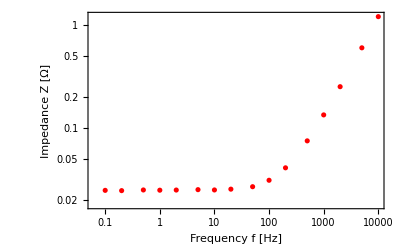

```mathematica
(* R-L-C model of the Zeeman Slower *)
ZSZmodelRLC = NonlinearModelFit[ZSfitdata, √(R^2+ (2π f L - 1/(2π f c))^2), {{R, 0.0026}, {L, 0.000003}, c}, f];
ZSZmodelRLC["BestFitParameters"] 
ZSZmodelRLC["ParameterConfidenceIntervals"]
Show[ListLogLogPlot[ZSZplotdata, PlotStyle->Red, PlotTheme->"Scientific", FrameLabel->{"Frequency f [Hz]", "Impedance Z [Ω]"}], LogLogPlot[ZSZmodelRLC[f], {f, 0, 12000}, PlotStyle->{Purple, Dashed}, PlotRange->All]]
```